# Importing data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
DetectionPoints = Import["DetectionPoints.dat"];
```

```mathematica
ReactionPoints = Import["ReactionPoints.dat"];
```

```mathematica
RecoilEnergies = Flatten[Import["RecoilEnergies.dat"]];
```

```mathematica
RecoilScatterAngles = Flatten[Import["RecoilScatterAngles.dat"]];
```

```mathematica
EjectEnergies = Flatten[Import["EjectileEnergies.dat"]];
```

```mathematica
EjectScatterAngles = Flatten[Import["EjectileScatterAngles.dat"]];
```

```mathematica
RecoilAnglesKinematics = Flatten[Import["RecoilAngles_Z_Axis.dat"]];
```

```mathematica
EjectScatterAnglesKinematics = Flatten[Import["EjectileAngles_Z_Axis.dat"]];
```

```mathematica
Biparametric = Import["BiParametric.dat"];
```

## Reaction points

```mathematica
ListPointPlot3D[ReactionPoints,AxesLabel->{Style[x[m],15,Black],Style[y[m],15,Black],Style[z[m],15,Black]}]
```

-Graphics3D-

## Detection points + reaction points

```mathematica
Show[ListPointPlot3D[Callout[Style[ReactionPoints,Black],Style["Alvo",14,Black,Bold],{0,0,2.67}],PlotStyle->PointSize[0.004]],ListPointPlot3D[Callout[Style[DetectionPoints,Red],Style["Detector",14,Black,Bold],{0,0.04,2.68}],PlotStyle->PointSize[0.004]],BoxRatios->{2,11,10},PlotRange-> {{-0.01,0.01},{-0.01,0.1},{2.6,2.7}},PlotStyle->Directive[Black,Thin],AxesLabel->{Style["y[m]",16,Black],Style["x[m]",16,Black],Style["z[m]",16,Black]},AxesStyle->Directive[Black,14]]
```

## Sec beam data

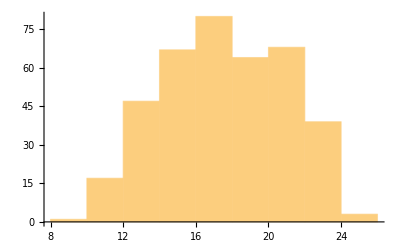

```mathematica
Histogram[EjectEnergies]
```

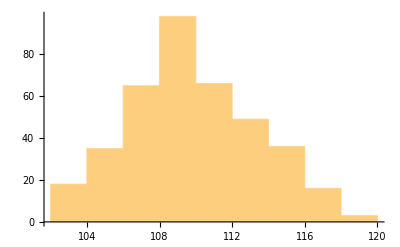

```mathematica
Histogram[EjectScatterAngles]
```

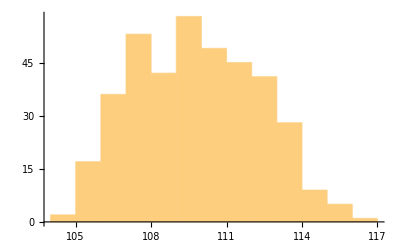

```mathematica
Histogram[EjectScatterAnglesKinematics]
```

## Recoil data

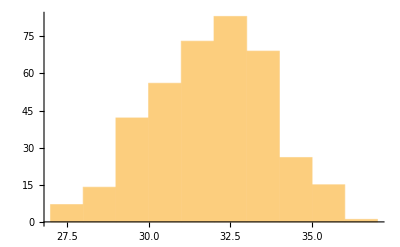

```mathematica
Histogram[RecoilScatterAngles]
```

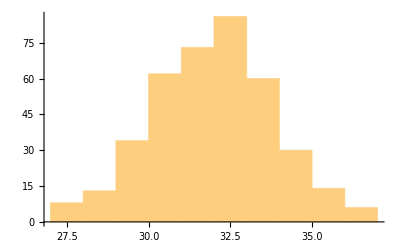

```mathematica
Histogram[RecoilAnglesKinematics]
```

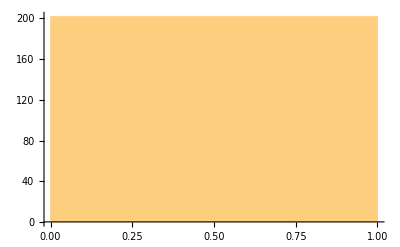

```mathematica
Histogram[RecoilEnergies]
```